```mathematica
Clear[dataEnergyPBC,dataEnergyOBC]
```

```mathematica
dataEnergyPBC=Import["EigenvaluesParent60Irrational6to12mM1PBC.dat"];
```

```mathematica
dataEnergyOBC=Import["EigenvaluesParent60Irrational6to12mM1OBC.dat"];
```

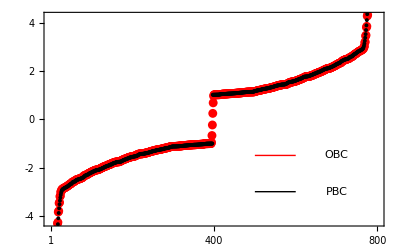

```mathematica
Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{0,800},{-4.25,4.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,400,800},None}},BaseStyle-> 18],

ListPlot[dataEnergyPBC,PlotStyle-> {Black,PointSize[0.007]}],

Plot[-1.5,{x,500,600},PlotStyle-> {Thick,Red}],
Plot[-3.0,{x,500,600},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{700,-1.5}],Inset["PBC",{700,-3.0}]}
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[LatticeIrrational,latticeRational]
```

```mathematica
LatticeIrrational=Table[{j,0},{j,1,396}];
```

```mathematica
latticeRational=Table[{j,0},{j,1,380}];
```

```mathematica
largestXRational = 380;
largestXIrrational = 396;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc]
```

```mathematica
dataLDoSPBC=Import["LDOSParent60Irrational6to12mM1PBC.dat"];
```

```mathematica
dataLDoSOBC=Import["LDOSParent60Irrational6to12mM1OBC.dat"];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@dataLDoSOBC[[All,3]]
```

{0,0.0773054}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"3.9"},{rng[[2]]-10^-3,"7.8"}}]
```

```mathematica
(** Crop appropriately and put the numbers in inkscape **)
```

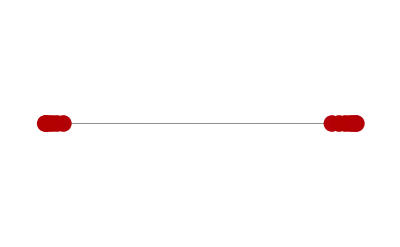

```mathematica
Show[
ListPlot[LatticeIrrational,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-10,405},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]
}&/@dataLDoSOBC,
BaseStyle-> 18
]

]
```